```mathematica
SetDirectory[NotebookDirectory[]];
stats=Import["../data/out/matching_stats.csv"];
```

```mathematica
chars=(StringTake[#,1]&/@FileNameTake/@stats[[All,1]]);
```

```mathematica
classes=LetterNumber/@chars;
```

```mathematica
colors=ColorData["Rainbow"]/@Rescale[Mod[classes,4]];
```

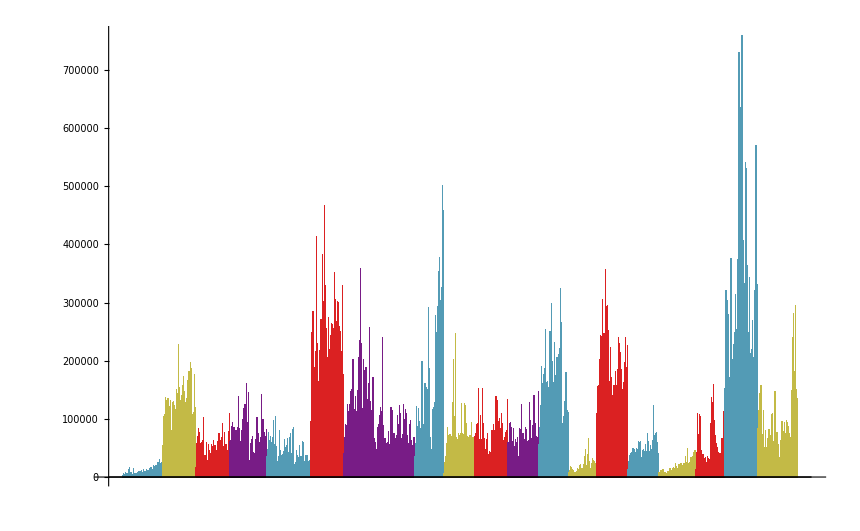

```mathematica
BarChart[stats[[All,2]],ChartStyle->colors]
```

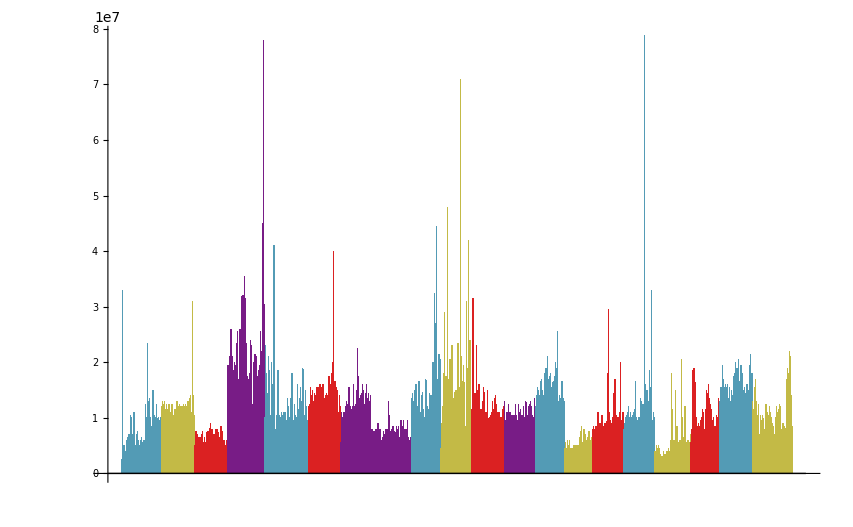

```mathematica
BarChart[stats[[All,4]],ChartStyle->colors]
```

```mathematica
DeleteDuplicates@chars
```

{a,b,c,d,e,g,h,l,m,n,o,p,q,r,s,u,v,w,y,z}